For the Max Graphon we need some assumptions to solve the integrals properly

```mathematica
$Assumptions=a>0 && b<1 && a<b &&  a<1 && b>0&&x>0 && x< 1 && y>0 && y<1
```

a>0&&b<1&&a<b&&a<1&&b>0&&x>0&&x<1&&y>0&&y<1

```mathematica
graphon[x_,y_] = 1 -Max[x,y]
k[x_] := Simplify[Integrate[graphon[x,y],{y,0,1}],x>=0 && x<=1]
mu:=Integrate[k[x],{x,0,1}]
P[x_,y_] := k[x]*k[y]/mu
```

1-Max[x,y]

Modularity surface

```mathematica
BM[x_,y_] = graphon[x,y] - 3*(x^2 - 1)*(y^2 - 1)/4
```

1-3/4 (-1+x^2) (-1+y^2)-Max[x,y]

Modularity slice

```mathematica
L[a_,b_]=Simplify[Integrate[Integrate[ 1-Max[x,y]-3/4 (-1+x^2) (-1+y^2),{y,a,b}],{x,a,b}]]
```

-1/12 (a-b)^2 (a^4+2 a^3 b+(-1+b)^3 (3+b)+3 a^2 (-2+b^2)+2 a (2-3 b+b^3))

For three communities the modularity is proportional to the following function. The free parameters are the positions of the borders x1 and x2. We obtain

```mathematica
Q3= L[0,x1] + L[x1,x2]+L[x2,1]
```

-1/12 (-1+x1)^3 x1^2 (3+x1)-1/12 (-1+x2)^2 (-3 x2^2+2 x2^3+x2^4)-1/12 (x1-x2)^2 (x1^4+2 x1^3 x2+(-1+x2)^3 (3+x2)+3 x1^2 (-2+x2^2)+2 x1 (2-3 x2+x2^3))

The modularity maximisation can then be solved with a two-dimensional optimisation procedure.

```mathematica
Maximize[{Q3,x1>0 && x2<1 && x1<x2},{x1,x2}]
```

{-Root-0.0197Root[134432259526656+30716568055215488 #1+2751343513100249664 #1^2+120367158096187119744 #1^3+2550512585505524791392 #1^4+19895664316728106040688 #1^5-32999893441632214846992 #1^6+12983573617806150722646 #1^7+5523451474061735271261 #1^8+713596501482279938136 #1^9+45912370178459515032 #1^10+1669291812588499920 #1^11+35203523717853072 #1^12+406363801230144 #1^13+2008387814976 #1^14&,4]-0.01968208461429507,{x1→Root0.369Root[{134432259526656+30716568055215488 #1+2751343513100249664 #1^2+120367158096187119744 #1^3+2550512585505524791392 #1^4+19895664316728106040688 #1^5-32999893441632214846992 #1^6+12983573617806150722646 #1^7+5523451474061735271261 #1^8+713596501482279938136 #1^9+45912370178459515032 #1^10+1669291812588499920 #1^11+35203523717853072 #1^12+406363801230144 #1^13+2008387814976 #1^14&,36864 #1^2+1880064 #1^3+82944 #1^4-110592 #1^2 #2+1161216 #1^3 #2+32256 #1 #2^2+2515968 #1^2 #2^2+259200 #1^3 #2^2-181248 #1 #2^3-4937472 #1^2 #2^3-470016 #1^3 #2^3+6912 #2^4+1431360 #1 #2^4+1239408 #1^2 #2^4+269568 #1^3 #2^4-56640 #2^5-5235552 #1 #2^5+2059776 #1^2 #2^5+344688 #2^6+8337702 #1 #2^6+«29»+9072 #1^2 #2^12+42924 #2^13+381024 #1 #2^13+986184 #2^14-73062 #1 #2^14-369692 #2^15-26352 #1 #2^15-238410 #2^16+14580 #1 #2^16+165780 #2^17+2304 #2^18-810 #1 #2^18-24300 #2^19+5184 #2^20+1188 #2^21-648 #2^22+27 #2^24&},{4,7}]0.36944688810736914,x2→Root0.463Root[{134432259526656+30716568055215488 #1+2751343513100249664 #1^2+120367158096187119744 #1^3+2550512585505524791392 #1^4+19895664316728106040688 #1^5-32999893441632214846992 #1^6+12983573617806150722646 #1^7+5523451474061735271261 #1^8+713596501482279938136 #1^9+45912370178459515032 #1^10+1669291812588499920 #1^11+35203523717853072 #1^12+406363801230144 #1^13+2008387814976 #1^14&,36864 #1^2+1880064 #1^3+82944 #1^4-110592 #1^2 #2+1161216 #1^3 #2+32256 #1 #2^2+2515968 #1^2 #2^2+259200 #1^3 #2^2-181248 #1 #2^3-4937472 #1^2 #2^3-470016 #1^3 #2^3+6912 #2^4+1431360 #1 #2^4+1239408 #1^2 #2^4+«38»+42924 #2^13+381024 #1 #2^13+986184 #2^14-73062 #1 #2^14-369692 #2^15-26352 #1 #2^15-238410 #2^16+14580 #1 #2^16+165780 #2^17+2304 #2^18-810 #1 #2^18-24300 #2^19+5184 #2^20+1188 #2^21-648 #2^22+27 #2^24&,-6 #1-3 #2^2+6 #2^3-6 #2^4+#2^6+3 #2 #3+3 #2^3 #3-3 #3^2-6 #2 #3^2+8 #3^3+3 #2 #3^3-#2^3 #3^3-6 #3^4+#3^6&},{4,7,4}]0.4633376818350991}}

```mathematica
ContourPlot[Q3,{x1,0,1},{x2,0,1},PlotLegends->Automatic]
```

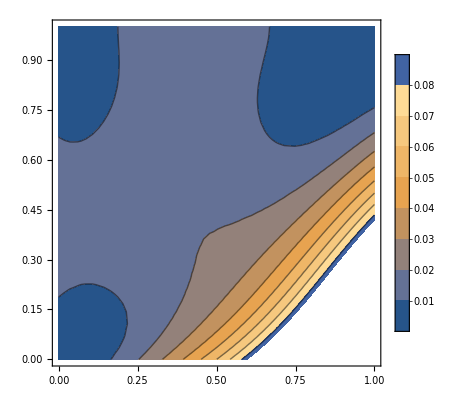

Check for two communities

```mathematica
Q2[x_]=Refine[L[0,x]+L[x,1]]
```

-1/12 (-1+x)^3 x^2 (3+x)-1/12 (-1+x)^2 (-3 x^2+2 x^3+x^4)

```mathematica
Maximize[{Q2,x1>0 && x1<1},{x1}]
```

{Q2,{x1→1/2}}

```mathematica
-1/12 (-1+x)^3 x^2 (3+x)-1/12 (-1+x)^2 (-3 x^2+2 x^3+x^4)
```